{20,35,50,75,100,150}

{{526.556,560.947,456.605,424.595,343.929,338.201,590.549,323.344,703.719,398.095,499.859,334.567,254.114,579.472,330.409,449.832,846.612,721.764,619.865,427.697},{321.765,467.672,479.927,257.841,441.624,242.064,385.161,86.313,80.98,71.562,245.332,463.796,96.024,668.263,100.589,142.905,248.339,527.547,275.083,270.189,144.3},{227.281,113.394,123.504,111.831,84.873,92.293,174.207,85.002,175.937,101.973},{79.14,107.529,89.672,102.332,118.648,74.725,95.211,80.041,65.896,63.093},{60.597,71.027,83.958,96.939,57.033,97.829,223.576,81.88,80.56,66.308},{42.506,56.769,55.777,44.714,97.077,73.739,70.794,79.889,115.628,103.22}}

{{72.181,73.895,184.933,137.726,143.83,147.676,93.775,164.611,76.171,74.38,124.307,103.166,436.978,242.923,93.456,201.714,458.818,159.175,89.401,103.069,77.416,213.125,119.876,145.832,268.768,231.005,94.334,191.861,104.442,294.406},{89.628,70.108,186.305,121.081,97.656,136.381,119.728,77.181,101.129,102.702,136.713,73.953,92.391,84.117,74.035,126.548,149.497,140.038,136.118,223.616,98.687,142.678,107.452,108.786,145.359,111.328,94.657,85.641,99.769,158.786},{100.405,140.185,79.429,106.242,136.012,82.852,105.1,209.077,91.367,84.89,136.713,73.953,92.391,84.117,74.035,126.548,149.497,140.038,136.118,223.616,118.71,88.957,126.567,77.769,75.929,76.603,140.051,101.785,69.3,105.819},{134.584,255.543,107.649,93.22,138.505,57.97,115.303,104.176,183.286,134.035,92.251,66.214,66.464,111.814,69.95,76.919,80.384,75.293,76.832,106.273,81.884,92.547,129.438,129.397,95.039,108.602,78.384,104.817,139.525,85.677},{105.568,93.642,121.171,106.749,104.62,114.764,142.019,155.79,90.058,80.366,55.473,70.327,85.823,83.939,128.285,84.928,94.669,72.741,140.879,51.772,85.115,102.33,52.541,208.345,110.582,66.21,96.083,121.967,103.819,63.374}}

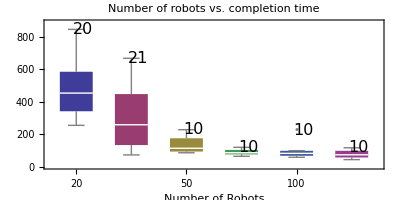

```mathematica
numberofRobots = {20,35,50,75,100,125,150}
newNumberControl = {{526.556,560.947,456.605,424.595,343.929,338.201,590.549,323.344,703.719,398.095,499.859,334.567,254.114,579.472,330.409,449.832,846.612,721.764,619.865,427.697},{321.765,467.672,479.927,(*1553.337,*)257.841,441.624,242.064,385.161,86.313,(*1429.706,*)80.98,71.562,(*1197.244,*)245.332,463.796,96.024,668.263,(*1746.615,*)100.589,142.905,248.339,527.547,275.083,270.189,(*1046.884,*)144.3},{227.281,113.394,123.504,111.831,84.873,92.293,174.207,85.002,175.937,101.973,72.181,73.895,184.933,137.726,143.83,147.676,93.775,164.611,76.171,74.38,124.307,103.166,436.978,242.923,93.456,201.714,458.818,159.175,89.401,103.069,77.416,213.125,119.876,145.832,268.768,231.005,94.334,191.861,104.442,294.406},{79.14,107.529,89.672,102.332,118.648,74.725,95.211,80.041,65.896,63.093},{60.597,71.027,83.958,96.939,57.033,97.829,223.576,81.88,80.56,66.308,100.405,140.185,79.429,106.242,136.012,82.852,105.1,209.077,91.367,84.89,136.713,73.953,92.391,84.117,74.035,126.548,149.497,140.038,136.118,223.616,118.71,88.957,126.567,77.769,75.929,76.603,140.051,101.785,69.3,105.819},
{134.584,255.543,107.649,93.22,138.505,57.97,115.303,104.176,183.286,134.035,92.251,66.214,66.464,111.814,69.95,76.919,80.384,75.293,76.832,106.273,81.884,92.547,129.438,129.397,95.039,108.602,78.384,104.817,139.525,85.677},
{42.506,56.769,55.777,44.714,97.077,73.739,70.794,79.889,115.628,103.22,105.568,93.642,121.171,106.749,104.62,114.764,142.019,155.79,90.058,80.366,55.473,70.327,85.823,83.939,128.285,84.928,94.669,72.741,140.879,51.772,85.115,102.33,52.541,208.345,110.582,66.21,96.083,121.967,103.819,63.374}}
cleanControl = {{72.181,73.895,184.933,137.726,143.83,147.676,93.775,164.611,76.171,74.38,124.307,103.166,436.978,242.923,93.456,201.714,458.818,159.175,89.401,103.069,77.416,213.125,119.876,145.832,268.768,231.005,94.334,191.861,104.442,294.406},{89.628,70.108,186.305,121.081,97.656,136.381,119.728,77.181,101.129,102.702,136.713,73.953,92.391,84.117,74.035,126.548,149.497,140.038,136.118,223.616,98.687,142.678,107.452,108.786,145.359,111.328,94.657,85.641,99.769,158.786},
{100.405,140.185,79.429,106.242,136.012,82.852,105.1,209.077,91.367,84.89,136.713,73.953,92.391,84.117,74.035,126.548,149.497,140.038,136.118,223.616,118.71,88.957,126.567,77.769,75.929,76.603,140.051,101.785,69.3,105.819},
{134.584,255.543,107.649,93.22,138.505,57.97,115.303,104.176,183.286,134.035,92.251,66.214,66.464,111.814,69.95,76.919,80.384,75.293,76.832,106.273,81.884,92.547,129.438,129.397,95.039,108.602,78.384,104.817,139.525,85.677},
{105.568,93.642,121.171,106.749,104.62,114.764,142.019,155.79,90.058,80.366,55.473,70.327,85.823,83.939,128.285,84.928,94.669,72.741,140.879,51.772,85.115,102.33,52.541,208.345,110.582,66.21,96.083,121.967,103.819,63.374}}


BoxWhiskerChart[newNumberControl,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},
ChartLabels->Placed[{numberofRobots,Length/@newNumberControl},{Axis,{.70,1}}],
AspectRatio->.5,
PlotLabel-> Style["Number of robots vs. completion time",FontSize->FontSz],
ChartStyle->1,ChartLabels->{StringForm[ "Time (s)"]},(*BarOrigin->Left,*)LabelStyle->FontSz,FrameLabel->{StringForm[ "Number of Robots"]}]
Export["../pictures/pdf/SimVeryNum.pdf",%];
```

```mathematica
{{72.181,73.895,184.933,137.726,143.83,147.676,93.775,164.611,76.171,74.38,124.307,103.166,436.978,242.923,93.456,201.714,458.818,159.175,89.401,103.069,77.416,213.125,119.876,145.832,268.768,231.005,94.334,191.861,104.442,294.406},{89.628,70.108,186.305,121.081,97.656,136.381,119.728,77.181,101.129,102.702,136.713,73.953,92.391,84.117,74.035,126.548,149.497,140.038,136.118,223.616,98.687,142.678,107.452,108.786,145.359,111.328,94.657,85.641,99.769,158.786},{100.405,140.185,79.429,106.242,136.012,82.852,105.1,209.077,91.367,84.89,136.713,73.953,92.391,84.117,74.035,126.548,149.497,140.038,136.118,223.616,118.71,88.957,126.567,77.769,75.929,76.603,140.051,101.785,69.3,105.819},{134.584,255.543,107.649,93.22,138.505,57.97,115.303,104.176,183.286,134.035,92.251,66.214,66.464,111.814,69.95,76.919,80.384,75.293,76.832,106.273,81.884,92.547,129.438,129.397,95.039,108.602,78.384,104.817,139.525,85.677},{105.568,93.642,121.171,106.749,104.62,114.764,142.019,155.79,90.058,80.366,55.473,70.327,85.823,83.939,128.285,84.928,94.669,72.741,140.879,51.772,85.115,102.33,52.541,208.345,110.582,66.21,96.083,121.967,103.819,63.374}}
```

{{72.181,73.895,184.933,137.726,143.83,147.676,93.775,164.611,76.171,74.38,124.307,103.166,436.978,242.923,93.456,201.714,458.818,159.175,89.401,103.069,77.416,213.125,119.876,145.832,268.768,231.005,94.334,191.861,104.442,294.406},{89.628,70.108,186.305,121.081,97.656,136.381,119.728,77.181,101.129,102.702,136.713,73.953,92.391,84.117,74.035,126.548,149.497,140.038,136.118,223.616,98.687,142.678,107.452,108.786,145.359,111.328,94.657,85.641,99.769,158.786},{100.405,140.185,79.429,106.242,136.012,82.852,105.1,209.077,91.367,84.89,136.713,73.953,92.391,84.117,74.035,126.548,149.497,140.038,136.118,223.616,118.71,88.957,126.567,77.769,75.929,76.603,140.051,101.785,69.3,105.819},{134.584,255.543,107.649,93.22,138.505,57.97,115.303,104.176,183.286,134.035,92.251,66.214,66.464,111.814,69.95,76.919,80.384,75.293,76.832,106.273,81.884,92.547,129.438,129.397,95.039,108.602,78.384,104.817,139.525,85.677},{105.568,93.642,121.171,106.749,104.62,114.764,142.019,155.79,90.058,80.366,55.473,70.327,85.823,83.939,128.285,84.928,94.669,72.741,140.879,51.772,85.115,102.33,52.541,208.345,110.582,66.21,96.083,121.967,103.819,63.374}}

{5,15,25,35,45}

{{53.965,72.084,61.723,100.14,90.616,83.261,126.401,131.031,113.948,60.417},{98.777,78.189,68.712,72.245,105.295,69.409,75.392,85.598,306.186,64.06},{62.185,83.31,94.26,85.235,122.3,124.345,98.842,90.476,70.277,68.342},{118.89,132.302,246.945,72.978,152.608,77.219,80.156,78.2,129.699,125.219},{105.207,95.445,107.618,214.17,170.141,89.349,86.596,99.944,116.99,142.071}}

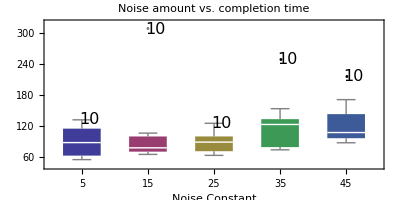

```mathematica
noise = {5,15,25,35,45}
noiseControlTime = {{53.965,72.084,61.723,100.14,90.616,83.261,126.401,131.031,113.948,60.417},{98.777,78.189,68.712,72.245,105.295,69.409,75.392,85.598,306.186,64.06},{62.185,83.31,94.26,85.235,122.3,124.345,98.842,90.476,70.277,68.342},{118.89,132.302,246.945,72.978,152.608,77.219,80.156,78.2,129.699,125.219},{105.207,95.445,107.618,214.17,170.141,89.349,86.596,99.944,116.99,142.071}}
BoxWhiskerChart[noiseControlTime,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},
ChartLabels->Placed[{noise,Length/@noiseControlTime},{Axis,{.70,1}}],
AspectRatio->.5,
PlotLabel-> Style["Noise amount vs. completion time",FontSize->FontSz],
ChartStyle->1,ChartLabels->varyControl⟦;;,1,1⟧,(*BarOrigin->Left,*)LabelStyle->FontSz,FrameLabel->{StringForm[ "Noise Constant"]}]
Export["../pictures/pdf/SimVeryNoise.pdf",%];
```

{0.5,1,1.5,2,3}

{{54.637,112.657,138.647,174.946,79.355,86.697,59.258,71.37,97,67.524},{83.881,101.291,140.773,93.858,163.338,83.808,112.73,115.514,203.163,82.469},{123.434,166.41,196.416,149.339,159.283,219.609,111.391,115.097,178.228,198.361},{142.191,154.44,183.777,169.579,141.689,144.104,211.664,143.337,234.123,199.646},{179.958,169.705,439.077,276.217,253.17,566.144,336.166,116.575,211.071,236.499}}

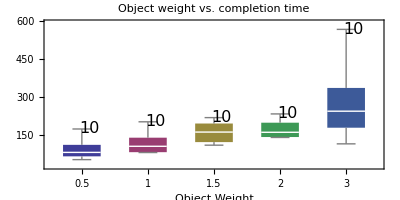

```mathematica
density = {0.5,1,1.5,2,3}
densityControlTime ={{54.637,112.657,138.647,174.946,79.355,86.697,59.258,71.37,97,67.524},{83.881,101.291,140.773,93.858,163.338,83.808,112.73,115.514,203.163,82.469},{123.434,166.41,196.416,149.339,159.283,219.609,111.391,115.097,178.228,198.361},{142.191,154.44,183.777,169.579,141.689,144.104,211.664,143.337,234.123,199.646},{179.958,169.705,439.077,276.217,253.17,566.144,336.166,116.575,211.071,236.499}}
BoxWhiskerChart[densityControlTime,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},
ChartLabels->Placed[{density,Length/@densityControlTime},{Axis,{.70,1}}],
AspectRatio->.5,
PlotLabel-> Style["Object weight vs. completion time",FontSize->FontSz],
ChartStyle->1,ChartLabels->varyControl⟦;;,1,1⟧,(*BarOrigin->Left,*)LabelStyle->FontSz,FrameLabel->{StringForm[ "Object Weight"]}]
Export["../pictures/pdf/SimVeryWeight.pdf",%];
```

{Circle,Hexagon,ShortRect,Square}

{{112.644,264.762,98.975,114.971,115.017,91.907,114.99,112.908,107.093,315.691},{90.11,122.266,117.807,155.806,94.328,90.305,123.718,80.09,83.057,92.494},{321.589,166.241,82.646,216.766,202.454,191.14,138.013,169.915,64.364,209.154},{270.547,131.131,290.865,188.28,99.628,170.493,222.561,164.781,168.944,266.253}}

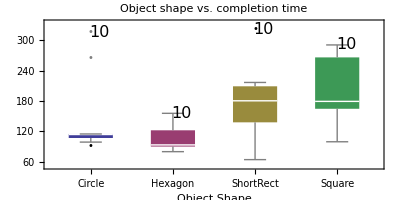

```mathematica
shapes ={Circle,Hexagon,  ShortRect,Square}
shapesControlTime = {{112.644,264.762,98.975,114.971,115.017,91.907,114.99,112.908,107.093,315.691},{90.11,122.266,117.807,155.806,94.328,90.305,123.718,80.09,83.057,92.494},
{321.589,166.241,82.646,216.766,202.454,191.14,138.013,169.915,64.364,209.154},{270.547,131.131,290.865,188.28,99.628,170.493,222.561,164.781,168.944,266.253}}
BoxWhiskerChart[shapesControlTime,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},
ChartLabels->Placed[{shapes,Length/@shapesControlTime},{Axis,{.70,1}}],
AspectRatio->.5,
PlotLabel-> Style["Object shape vs. completion time",FontSize->FontSz],
ChartStyle->1,ChartLabels->varyControl⟦;;,1,1⟧,(*BarOrigin->Left,*)LabelStyle->FontSz,FrameLabel->{StringForm[ "Object Shape"]}]
Export["../pictures/pdf/SimVeryShape.pdf",%];
```